```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Plot E1 threshold as a function of f0*)
```

```mathematica
(*we remove points that fail to converge to finite value, so the threshold is simply the largest E1 in the dataset*)
getThreshold[points_]:=Module[{},

thisn1=points[[1]];
e0Values=thisn1[[;;,1]]//Sort;
threshold=e0Values[[-1]]
]
```

```mathematica
f0List={1,0.1,0.01,0.001,0.0001,0.00001};
```

```mathematica
dataPairs={};
```

```mathematica
For[i=1,i<=Length[f0List],i++,

thisf0=f0List[[i]];
thisFilename="id_data_fi_1//integratedDecoyPoints_f0_"<>ToString[thisf0]<>"_fi_1_n1tan2.mx";
thisFile=Import[thisFilename];

thisThreshold=getThreshold[thisFile];

AppendTo[dataPairs,{thisf0,thisThreshold}];

]
```

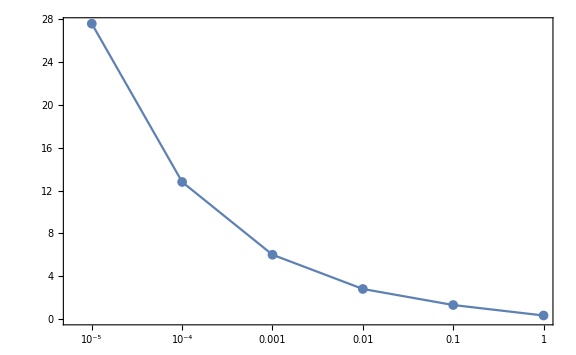

```mathematica
ListLogLinearPlot[dataPairs,Frame->{True,True,False,False},(*FrameLabel->{"n_1 self-interaction f_0","Activating effector load E_1^*"},*)LabelStyle->Directive[Black, 25],ImageSize->Large,Joined->True,PlotMarkers->{Automatic,Medium}]
```

```mathematica
(*Export["integratedDecoy_fi_1_f0Plot.png",%,ImageResolution->200];*)
```